```mathematica
<<PlotLegends`
```

```mathematica
pata120161128=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\pata\\1_20161128.xlsx"];
pata220161128=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\pata\\2_20161128.xlsx"];
pata320161128=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\pata\\3_20161128.xlsx"];
pata420161128=Import["C:\\Users\\renan\\Desktop\\622\\spreadsheets\\modified\\pata\\4_20161128.xlsx"];
```

```mathematica
tempo=Table[pata120161128[[1,i,1]],{i,1,Length[pata120161128[[1]]]}];
```

```mathematica
transp120161128=Table[pata120161128[[1,i,2]],{i,1,Length[tempo]}];
transp220161128=Table[pata220161128[[1,i,2]],{i,1,Length[tempo]}];
transp320161128=Table[pata320161128[[1,i,2]],{i,1,Length[tempo]}];
transp420161128=Table[pata420161128[[1,i,2]],{i,1,Length[tempo]}];
```

```mathematica
par120161128=Table[pata120161128[[1,i,3]],{i,1,Length[tempo]}];
par220161128=Table[pata220161128[[1,i,3]],{i,1,Length[tempo]}];
par320161128=Table[pata320161128[[1,i,3]],{i,1,Length[tempo]}];
par420161128=Table[pata420161128[[1,i,3]],{i,1,Length[tempo]}];
```

```mathematica
dpv120161128=Table[pata120161128[[1,i,4]],{i,1,Length[tempo]}];
dpv220161128=Table[pata220161128[[1,i,4]],{i,1,Length[tempo]}];
dpv320161128=Table[pata320161128[[1,i,4]],{i,1,Length[tempo]}];
dpv420161128=Table[pata420161128[[1,i,4]],{i,1,Length[tempo]}];
```

```mathematica
transpVsTempo120161128=N[Table[{tempo[[i]],transp120161128[[i]]},{i,1,Length[tempo]}]];
transpVsTempo220161128=N[Table[{tempo[[i]],transp220161128[[i]]},{i,1,Length[tempo]}]];
transpVsTempo320161128=N[Table[{tempo[[i]],transp320161128[[i]]},{i,1,Length[tempo]}]];
transpVsTempo420161128=N[Table[{tempo[[i]],transp420161128[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
parVsTempo120161128=N[Table[{tempo[[i]],par120161128[[i]]},{i,1,Length[tempo]}]];
parVsTempo220161128=N[Table[{tempo[[i]],par220161128[[i]]},{i,1,Length[tempo]}]];
parVsTempo320161128=N[Table[{tempo[[i]],par320161128[[i]]},{i,1,Length[tempo]}]];
parVsTempo420161128=N[Table[{tempo[[i]],par420161128[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
dpvVsTempo120161128=N[Table[{tempo[[i]],dpv120161128[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo220161128=N[Table[{tempo[[i]],dpv220161128[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo320161128=N[Table[{tempo[[i]],dpv320161128[[i]]},{i,1,Length[tempo]}]];
dpvVsTempo420161128=N[Table[{tempo[[i]],dpv420161128[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobrePAR120161128=Table[transp120161128[[i]]/par120161128[[i]],{i,2,Length[tempo]-1}];
transpSobrePAR220161128=Table[transp220161128[[i]]/par220161128[[i]],{i,2,Length[tempo]-1}];
transpSobrePAR320161128=Table[transp320161128[[i]]/par320161128[[i]],{i,2,Length[tempo]-1}];transpSobrePAR420161128=Table[transp420161128[[i]]/par420161128[[i]],{i,2,Length[tempo]-1}];
```

```mathematica
transpSobrePARVsTempo120161128=N[Table[{tempo[[i]],transpSobrePAR120161128[[i]]},{i,1,Length[tempo]}]];
transpSobrePARVsTempo220161128=N[Table[{tempo[[i]],transpSobrePAR220161128[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo320161128=N[Table[{tempo[[i]],transpSobrePAR320161128[[i]]},{i,1,Length[tempo]}]];transpSobrePARVsTempo420161128=N[Table[{tempo[[i]],transpSobrePAR420161128[[i]]},{i,1,Length[tempo]}]];
```

```mathematica
transpSobreDPV120161128=Table[transp120161128[[i]]/dpv120161128[[i]],{i,1,Length[tempo]}];
transpSobreDPV220161128=Table[transp220161128[[i]]/dpv220161128[[i]],{i,1,Length[tempo]}];
transpSobreDPV320161128=Table[transp320161128[[i]]/dpv320161128[[i]],{i,1,Length[tempo]}];transpSobreDPV420161128=Table[transp420161128[[i]]/dpv420161128[[i]],{i,1,Length[tempo]}];
```

```mathematica
transpSobreDPVVsTempo120161128=N[Table[{tempo[[i]],transpSobreDPV120161128[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo220161128=N[Table[{tempo[[i]],transpSobreDPV220161128[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo320161128=N[Table[{tempo[[i]],transpSobreDPV320161128[[i]]},{i,1,Length[tempo]}]];
transpSobreDPVVsTempo420161128=N[Table[{tempo[[i]],transpSobreDPV420161128[[i]]},{i,1,Length[tempo]}]];
```

## Pata - 28/11/2016 - Transpiração

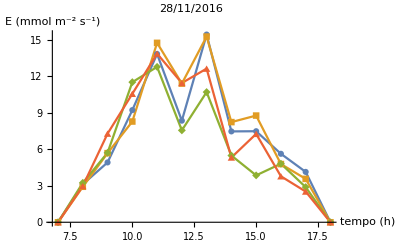

```mathematica
g1=ListLinePlot[{transpVsTempo120161128,transpVsTempo220161128,transpVsTempo320161128,transpVsTempo420161128},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.13MPa"},LegendPosition->{.7,-0.4},PlotLabel->"28/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E (mmol m^-2 s^-1)"}]
```

## Pata - 28/11/2016 - PAR ( radiação fotossinteticamente ativa)

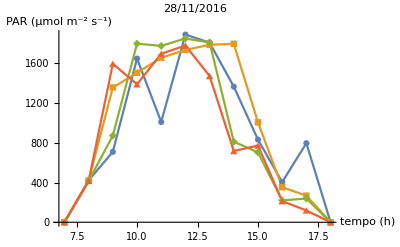

```mathematica
g2=ListLinePlot[{parVsTempo120161128,parVsTempo220161128,parVsTempo320161128,parVsTempo420161128},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.13MPa"},LegendPosition->{.7,-0.4},PlotLabel->"28/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","PAR (μmol m^-2 s^-1)"}]
```

## Pata - 28/11/2016 - DPV (déficit de pressão de vapor)

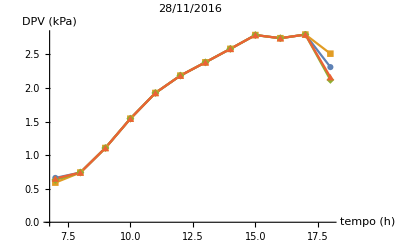

```mathematica
g3=ListLinePlot[{dpvVsTempo120161128,dpvVsTempo220161128,dpvVsTempo320161128,dpvVsTempo420161128},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.13MPa"},LegendPosition->{.7,-0.4},PlotLabel->"28/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","DPV (kPa)"}]
```

## Pata - 28/11/2016 - Relação Transpiração - PAR

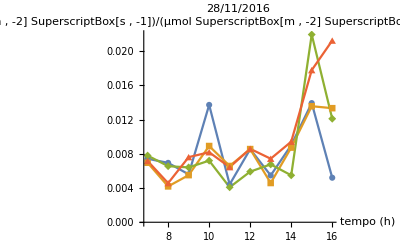

```mathematica
g4=ListLinePlot[{transpSobrePARVsTempo120161128,transpSobrePARVsTempo220161128,transpSobrePARVsTempo320161128,transpSobrePARVsTempo420161128},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.13MPa"},LegendPosition->{.7,-0.4},PlotLabel->"28/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/PAR ((mol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/(μmol SuperscriptBox[m , -2] SuperscriptBox[s , -1]))"}]
```

## Pata - 28/11/2016 - Relação Transpiração - DPV

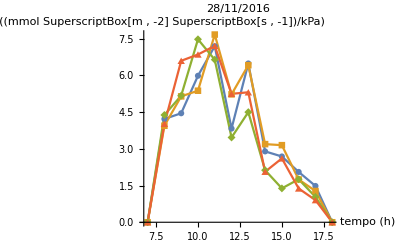

```mathematica
g5=ListLinePlot[{transpSobreDPVVsTempo120161128,transpSobreDPVVsTempo220161128,transpSobreDPVVsTempo320161128,transpSobreDPVVsTempo420161128},PlotLegend->{"-0.09MPa","-0.10MPa","-0.11MPa","-0.13MPa"},LegendPosition->{.7,-0.4},PlotLabel->"28/11/2016",Joined->{True,True,True},PlotMarkers->Automatic,AxesLabel->{"tempo (h)","E/DPV ((mmol SuperscriptBox[m , -2] SuperscriptBox[s , -1])/kPa)"}]
```